### Data

```mathematica
unitDirectory="C:\\Users\\..."
(*Path to directory that has units from a recording session (1 text file per unit containing a single list of spike times in seconds).
Example data: TV145
```

```mathematica
dataThetaEpochs=Import["C:\\Users\\...\\TV145-LHS-842um-L3_epochs.txt","Data"]
(*Path to directory that has list of theta epochs for the recording session (a text file with a matrix containing start and end time in seconds for each theta epoch)
```

{{56.0794,177.869},{189.8,308.942},{339.276,348.873},{352.031,355.782},{358.138,377.377},{383.541,405.843},{415.762,430.404},{466.155,485.988},{555.081,581.001}}

```mathematica
dataThetaTroughs=Flatten[Import["C:\\Users\\...\\TV145-LHS-842um-L3_units_thloc_troughs.txt","Data"]];
(*Path to directory that has list of theta trough times for the recording session (a text file containing a single list of trough times in seconds)
```

```mathematica
unitNames=StringTake[FileNames["unit"<>"*.txt",unitDirectory],{-18,-5}]
(*adjust the last two values so that you name each unit properly
```

{unit0024_final,unit0031_final,unit0072_final,unit0097_final,unit0134_final,unit0180_final,unit0206_final,unit0222_final,unit0623_final,unit0748_final,unit0766_final,unit0798_final,unit0800_final,unit0958_final,unit1016_final,unit1236_final,unit1239_final,unit1276_final,unit1298_final,unit1327_final,unit1480_final,unit1528_final,unit1533_final,unit1560_final,unit1563_final,unit1579_final,unit1678_final,unit1777_final,unit1779_final,unit1782_final}

```mathematica
dataUnits=Flatten/@Import[unitDirectory<>"unit"<>"*.txt","Table"];
(*dataUnits contains the data for each unit
```

### Functions

```mathematica
epochTroughs[epochList_,troughsList_]:=Table[Select[troughsList,epochList[[epoch,1]]<#<epochList[[epoch,2]]&],{epoch,1,Length[epochList]}]
```

```mathematica
epochSpikes[epochTroughsList_,spikesList_]:=Table[Select[spikesList,epochTroughsList[[epoch,1]]<#<epochTroughsList[[epoch,-1]]&],{epoch,1,Length[epochTroughsList]}]
```

```mathematica
spikePhasesEpochs[spikesListEpochs_,troughsListEpochs_]:=Table[360 ((spikesListEpochs⟦epoch⟧⟦spike⟧-#)/(Nearest[Cases[troughsListEpochs⟦epoch⟧,x_/;x>spikesListEpochs⟦epoch⟧⟦spike⟧],spikesListEpochs⟦epoch⟧⟦spike⟧]⟦1⟧-#))&[Nearest[Cases[troughsListEpochs⟦epoch⟧,x_/;x<spikesListEpochs⟦epoch⟧⟦spike⟧],spikesListEpochs⟦epoch⟧⟦spike⟧]⟦1⟧],{epoch,1,Length[troughsListEpochs]},{spike,1,Length[spikesListEpochs⟦epoch⟧]}]
```

```mathematica
Off[General::munfl]
```

```mathematica
convertDegreesToRadians[phasesListDegrees_]:=phasesListDegrees (π/180)
```

```mathematica
convertRadiansToDegrees[phasesListRadians_]:=phasesListRadians (180/π)
```

```mathematica
meanVector[phasesListRadians_]:={Mean[Sin[phasesListRadians]],Mean[Cos[phasesListRadians]]}
```

```mathematica
vectorLength[meanVector_]:=Sqrt[meanVector⟦1⟧^2+meanVector⟦2⟧^2]
```

```mathematica
meanAngleRadians[meanVector_]:=If[#<0,2 π+#,#]&[ArcTan[meanVector⟦2⟧,meanVector⟦1⟧]]
```

```mathematica
circularSD[vectorLength_]:=Sqrt[-2 Log[vectorLength]]
```

```mathematica
circularData[phasesListRadians_]:={{"Vector length (r)","Mean angle (deg)","Circular SD (deg)","Rayleigh test stat (Z)","P-value","n (spikes)"},{vectorLength[meanVector[phasesListRadians]],convertRadiansToDegrees[meanAngleRadians[meanVector[phasesListRadians]]],convertRadiansToDegrees[circularSD[vectorLength[meanVector[phasesListRadians]]]],#,Exp[-#],Length[phasesListRadians]}&[Length[phasesListRadians] vectorLength[meanVector[phasesListRadians]]^2]}
```

```mathematica
spikePhasesDegreesAllCells[spikesCellsList_,epochList_,troughsList_]:=With[{troughs=epochTroughs[epochList,troughsList]},Table[Flatten[spikePhasesEpochs[epochSpikes[troughs,spikesCellsList⟦spikesList⟧],troughs]],{spikesList,1,Length[spikesCellsList]}]]
```

### All cells from session

```mathematica
allCellsPhases=spikePhasesDegreesAllCells[dataUnits,dataThetaEpochs,dataThetaTroughs];
```

```mathematica
allCellsCircularData=Table[circularData[convertDegreesToRadians[allCellsPhases][[cell]]],{cell,1,Length[allCellsPhases]}];
```

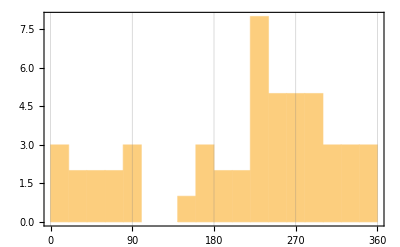
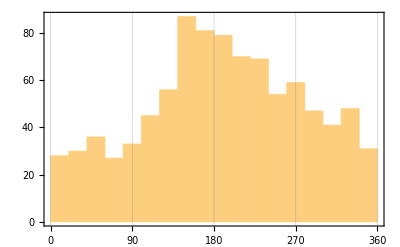
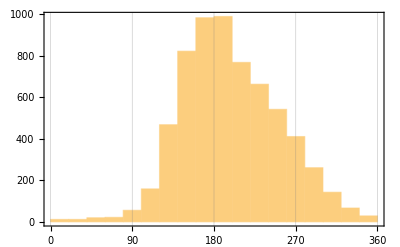
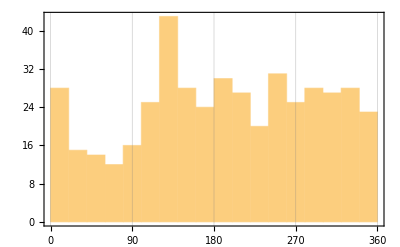
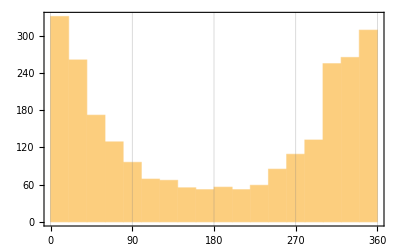
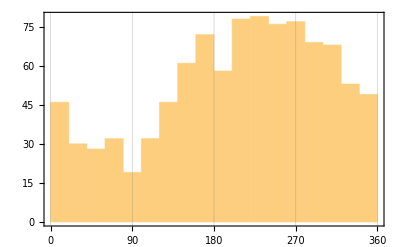
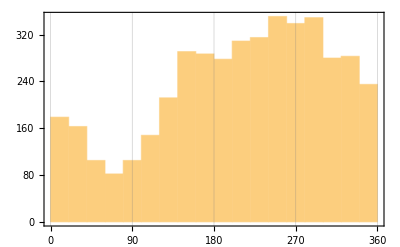
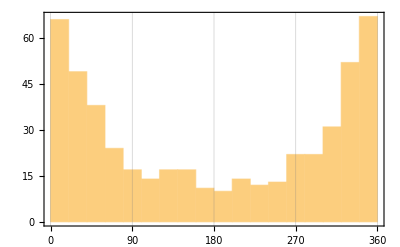

```mathematica
Table[Histogram[allCellsPhases⟦i⟧,20,Frame->True,FrameTicks->{{Automatic,None},{{0,90,180,270,360},None}},GridLines->{{0,90,180,270,360},None}],{i,1,Length[allCellsPhases]}]
(*Histograms of the spike counts in 20 degree bins
```

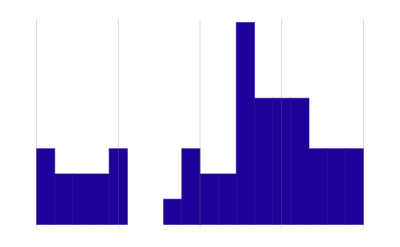
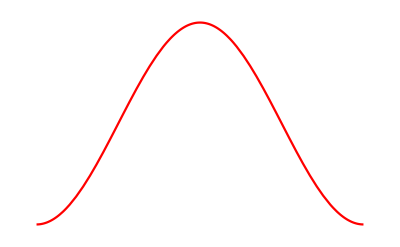
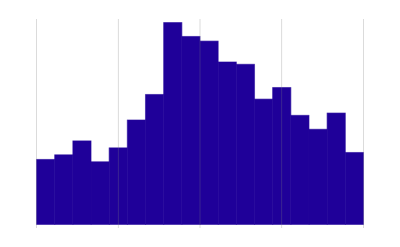
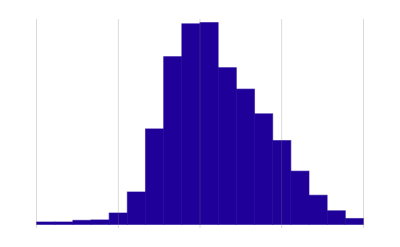
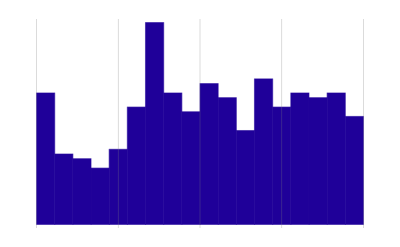
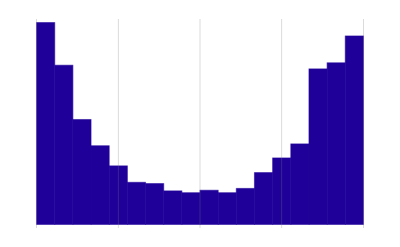
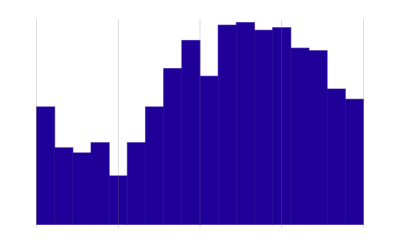
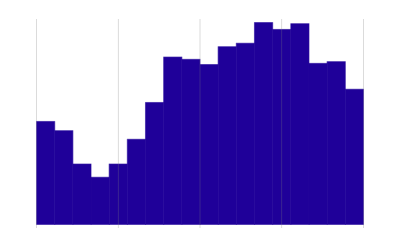
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Table[Overlay[{Histogram[allCellsPhases⟦i⟧,20,Frame->False,Axes->False,GridLines->{{0,90,180,270,360},None},ChartStyle->Hue[0.7,1,0.6]],Plot[Cos[x],{x,-π,π},Axes->False,PlotStyle->Red]}],{i,1,Length[allCellsPhases]}]
(*An overlay of an idealized theta cycle, with 180 degrees as the peak
```

```mathematica
circularDataTable=Table[Prepend[Transpose[allCellsCircularData][[2,cell]],unitNames[[cell]]],{cell,1,Length[unitNames
]}];
```

```mathematica
Export[unitDirectory<>"circularData.txt",circularDataTable,"Table"]
(*Exports the circular statistics data to the directory that contains the units
```

```mathematica
Prepend[Transpose[allCellsCircularData][[1,1]],"Unit"]
```

{Unit,Vector length (r),Mean angle (deg),Circular SD (deg),Rayleigh test stat (Z),P-value,n (spikes)}

```mathematica
circularDataTable//TableForm
```

unit0024_final | 0.338852 | 275.579 | 84.2926 | 5.97068 | 0.0025525 | 52
unit0031_final | 0.237787 | 199.171 | 97.1119 | 52.0757 | 2.41999×10^-23 | 921
unit0072_final | 0.648894 | 196.712 | 53.2873 | 2706.18 | 0. | 6427
unit0097_final | 0.0967091 | 222.131 | 123.845 | 4.15258 | 0.0157238 | 444
unit0134_final | 0.441026 | 355.511 | 73.314 | 496.764 | 1.81187×10^-216 | 2554
unit0180_final | 0.242003 | 243.833 | 96.5159 | 56.9841 | 1.7869×10^-25 | 973
unit0206_final | 0.243133 | 247.294 | 96.3573 | 254.84 | 2.11107×10^-111 | 4311
unit0222_final | 0.412583 | 2.41963 | 76.2407 | 84.4316 | 2.14695×10^-37 | 496
unit0623_final | 0.413315 | 336.895 | 76.1644 | 2.73327 | 0.0650061 | 16
unit0748_final | 0.310626 | 221.798 | 87.6144 | 2.99115 | 0.0502297 | 31
unit0766_final | 0.265408 | 238.475 | 93.3232 | 309.025 | 6.19377×10^-135 | 4387
unit0798_final | 0.252279 | 18.6594 | 95.0909 | 6.04625 | 0.00236671 | 95
unit0800_final | 0.0580758 | 320.417 | 136.696 | 0.0438464 | 0.957101 | 13
unit0958_final | 0.0554621 | 172.652 | 137.797 | 1.05816 | 0.347094 | 344
unit1016_final | 0.145106 | 262.91 | 112.577 | 91.1287 | 2.65036×10^-40 | 4328
unit1236_final | 0.151195 | 356.217 | 111.372 | 3.31467 | 0.036346 | 145
unit1239_final | 0.34222 | 227.4 | 83.9066 | 52.3502 | 1.83908×10^-23 | 447
unit1276_final | 0.873447 | 255.922 | 29.8057 | 2.28873 | 0.101395 | 3
unit1298_final | 0.296936 | 233.268 | 89.2873 | 26.1867 | 4.23883×10^-12 | 297
unit1327_final | 0.587261 | 210.975 | 59.1167 | 4.1385 | 0.0159467 | 12
unit1480_final | 0.12673 | 211.701 | 116.458 | 4.07936 | 0.0169183 | 254
unit1528_final | 0.182096 | 163.806 | 105.748 | 2.55323 | 0.0778299 | 77
unit1533_final | 0.420972 | 285.613 | 75.369 | 7.97479 | 0.000344026 | 45
unit1560_final | 0.198361 | 196.283 | 103.058 | 15.8176 | 1.35053×10^-7 | 402
unit1563_final | 0.129657 | 280.679 | 115.813 | 72.2868 | 4.03856×10^-32 | 4300
unit1579_final | 0.494858 | 207.363 | 67.9618 | 4.89769 | 0.00746378 | 20
unit1678_final | 0.25144 | 261.177 | 95.2059 | 5.81644 | 0.00297818 | 92
unit1777_final | 0.267138 | 262.634 | 93.0943 | 231.358 | 3.33006×10^-101 | 3242
unit1779_final | 0.358601 | 253.707 | 82.0569 | 574.946 | 2.01359×10^-250 | 4471
unit1782_final | 0.0968238 | 213.386 | 123.814 | 54.8241 | 1.54956×10^-24 | 5848

Smallest sample size:

```mathematica
Min[circularDataTableᵀ[[-1]]]
```

3

Mean angle for all cells in session (degrees) [this assumes the reference site for theta was in SP/SO and not below!]:

```mathematica
convertRadiansToDegrees[meanAngleRadians[meanVector[convertDegreesToRadians[circularDataTableᵀ[[3]]]]]]
```

247.01

Circular SD for all cells in session (degrees):

```mathematica
convertRadiansToDegrees[circularSD[vectorLength[meanVector[convertDegreesToRadians[circularDataTableᵀ[[3]]]]]]]
```

57.3266

Polar plot all units in session:

```mathematica
ListPolarPlot[Thread[{convertDegreesToRadians[circularDataTableᵀ[[3]]],circularDataTableᵀ[[2]]}],PolarAxes->True,PlotRange->All,PolarGridLines->{{0,Pi/2,Pi,3Pi/2},{0.1,0.2,0.3,0.4}},PolarTicks->{"Degrees",Range[0.1,0.6,0.1]},AspectRatio->Automatic,PlotRangePadding->0.25,PlotLabel->"Preferred theta phase (degrees) vs. vector length (r)",PlotStyle->Directive[PointSize[0.02],Hue[0.7,1,0.6]]]
```

-Graphics-

Distribution of vector lengths:

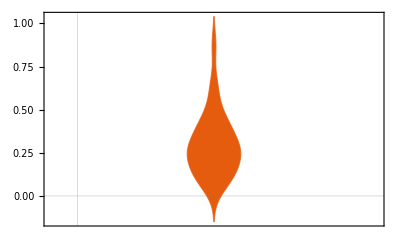

```mathematica
DistributionChart[circularDataTableᵀ[[2]],PlotTheme->"Scientific"]
```

```mathematica
Median[circularDataTableᵀ[[2]]]
```

0.258843

```mathematica
InterquartileRange[circularDataTableᵀ[[2]]]
```

0.261389

```mathematica
Min[circularDataTableᵀ[[2]]]
```

0.0554621

```mathematica
Max[circularDataTableᵀ[[2]]]
```

0.873447

Number and proportion (percentage) of significantly theta coupled units:

```mathematica
Length[Select[circularDataTableᵀ[[-2]],#<0.05&]]
```

24

```mathematica
Length[Select[circularDataTableᵀ[[-2]],#>0.05&]]
```

6

```mathematica
N[Length[Select[circularDataTableᵀ[[-2]],#<0.05&]]/Length[circularDataTableᵀ[[-2]]]] 100
```

80.